```mathematica
SetDirectory["Projects/Wolfram/Retention_Visualization/"]
```

```mathematica
"/Users/erichegonzales/Projects/Wolfram/Retention_Visualization"
```

/Users/erichegonzales/Projects/Wolfram/Retention_Visualization

```mathematica
springSaturday= Import["Spring_Bball101/Spring_Saturday.csv", "CSV"];
springSunday=Import["Spring_Bball101/Spring_Sunday.csv","CSV"];
springTuesday=Import["Spring_Bball101/Spring_Tuesday.csv","CSV"];
springThursday=Import["Spring_Bball101/Spring_Thursday.csv","CSV"];
```

```mathematica
winterSaturday=Import["Winter_Bball101/Winter_Saturday.csv","CSV"];
winterSunday=Import["Winter_Bball101/Winter_Sunday.csv","CSV"];
winterTuesday=Import["Winter_Bball101/Winter_Tuesday.csv","CSV"];
winterThursday=Import["Winter_Bball101/Winter_Thursday.csv","CSV"];
```

```mathematica
winterSaturday = DeleteCases[winterSaturday,{}];
winterSunday=DeleteCases[winterSunday,{}];
winterTuesday=DeleteCases[winterTuesday,{}];
winterThursday=DeleteCases[winterThursday,{}];
```

```mathematica
springSaturday=DeleteCases[springSaturday,{}];
springSunday=DeleteCases[springSunday,{}];
springTuesday=DeleteCases[springTuesday,{}];
springThursday=DeleteCases[springThursday,{}];
```

```mathematica
winterSaturday
```

{{teamid,teamname,customerid,firstname,lastname,email,phone,what school does your child attend?},{6036,[BBall 101] Saturday 9:00am-9:50am (Ages 4-6),59704,Benjamin,Babazadeh,jchudow@gmail.com,9144439712,},{6036,[BBall 101] Saturday 9:00am-9:50am (Ages 4-6),67886,Ryan,Doolan,CDoolan1234@gmail.com,9174941563,PS 527},{6036,[BBall 101] Saturday 9:00am-9:50am (Ages 4-6),67948,Filip,Florea,mugur.florea@gmail.com,2016184049,Collegiate},{6036,[BBall 101] Saturday 9:00am-9:50am (Ages 4-6),67949,Luca,Florea,mugur.florea@gmail.com,2016184049,West Side Montessori School},{6036,[BBall 101] Saturday 9:00am-9:50am (Ages 4-6),53391,Max,Friedman,rebecca.kaden@gmail.com,9175970557,92Y},{6036,[BBall 101] Saturday 9:00am-9:50am (Ages 4-6),61230,Mia,Itskowitch,kchessler@hotmail.com,2012806727,towns},{6036,[BBall 101] Saturday 9:00am-9:50am (Ages 4-6),60156,Kiyaan,Joshi,sanoushirvani@gmail.com,9176018020,St Davids},{6036,[BBall 101] Saturday 9:00am-9:50am (Ages 4-6),67790,Giovanni,Larrea,christopher.larrea@yahoo.com,6469192132,district 2 pre k center},{6036,[BBall 101] Saturday 9:00am-9:50am (Ages 4-6),67514,Samuel (Sam),Millette,millette.amy@gmail.com,,St David’s},{6036,[BBall 101] Saturday 9:00am-9:50am (Ages 4-6),65688,Grayson,Moskowitz,ddudick@gmail.com,7625981863,n/a},{6036,[BBall 101] Saturday 9:00am-9:50am (Ages 4-6),64325,Ava,Nejat,edwardnejat@gmail.com,9173011178,towns},{6036,[BBall 101] Saturday 9:00am-9:50am (Ages 4-6),65499,Tristan,Peake,kjpctp@gmail.com,9174029484,Playhouse},{6036,[BBall 101] Saturday 9:00am-9:50am (Ages 4-6),65501,Damian,Piuzzi Arvizo,Bpiuzzi@gmail.com,2162551703,District 30 pre-k center},{6036,[BBall 101] Saturday 9:00am-9:50am (Ages 4-6),67193,Joey Jr.,Rallo,bsmokler@efhutton.com,9178555924,st davids},{6036,[BBall 101] Saturday 9:00am-9:50am (Ages 4-6),67270,Ben,Reiss,Elizabeth.right@gmail.com,3039183140,Trinity},{6036,[BBall 101] Saturday 9:00am-9:50am (Ages 4-6),67271,Jake,Reiss,Elizabeth.right@gmail.com,3039183140,Trinity},{6036,[BBall 101] Saturday 9:00am-9:50am (Ages 4-6),53366,Sam,Tarkan,erwashkowitz@mac.com,9173715200,n/a},{6036,[BBall 101] Saturday 9:00am-9:50am (Ages 4-6),68405,Max,Teigman,lauras104@gmail.com,5163171622,N/A},{6036,[BBall 101] Saturday 9:00am-9:50am (Ages 4-6),65250,Alexander,Vandooijeweert,kaya.endo@gmail.com,9178085245,n/a}}

```mathematica
Grid[%142]
```

remove column 1 from all tables

```mathematica
springSaturday=springSaturday[[All,2;;]];
springSunday=springSunday[[All,2;;]];
springTuesday=springTuesday[[All,2;;]];
springThursday=springThursday[[All,2;;]];

winterSaturday=winterSaturday[[All,2;;]];
winterSunday=winterSunday[[All,2;;]];
winterTuesday=winterTuesday[[All,2;;]];
winterThursday=winterThursday[[All,2;;]];
```

remove all the first rows

```mathematica
springSaturday=springSaturday[[2;;,All]];
springSunday=springSunday[[2;;,All]];
springTuesday=springTuesday[[2;;,All]];
springThursday=springThursday[[2;;,All]];

winterSaturday=winterSaturday[[2;;,All]];
winterSunday=winterSunday[[2;;,All]];
winterTuesday=winterTuesday[[2;;,All]];
winterThursday=winterThursday[[2;;,All]];
```

```mathematica
satFullNames = Map[StringJoin[#[[1]], " ", #[[2]]] &, springSaturday[[All, {3, 4}]]];
springSaturday = MapThread[Append, {springSaturday, satFullNames}];

sunFullNames = Map[StringJoin[#[[1]], " ", #[[2]]] &, springSunday[[All, {3, 4}]]];
springSunday = MapThread[Append, {springSunday, sunFullNames}];

tueFullNames = Map[StringJoin[#[[1]], " ", #[[2]]] &, springTuesday[[All, {3, 4}]]];
springTuesday = MapThread[Append, {springTuesday, tueFullNames}];

thuFullNames = Map[StringJoin[#[[1]], " ", #[[2]]] &, springThursday[[All, {3, 4}]]];
springThursday = MapThread[Append, {springThursday, thuFullNames}];

satFullNames = Map[StringJoin[#[[1]], " ", #[[2]]] &, winterSaturday[[All, {3, 4}]]];
winterSaturday = MapThread[Append, {winterSaturday, satFullNames}];

sunFullNames = Map[StringJoin[#[[1]], " ", #[[2]]] &, winterSunday[[All, {3, 4}]]];
winterSunday = MapThread[Append, {winterSunday, sunFullNames}];

tueFullNames = Map[StringJoin[#[[1]], " ", #[[2]]] &, winterTuesday[[All, {3, 4}]]];
winterTuesday = MapThread[Append, {winterTuesday, tueFullNames}];

thuFullNames = Map[StringJoin[#[[1]], " ", #[[2]]] &, winterThursday[[All, {3, 4}]]];
winterThursday = MapThread[Append, {winterThursday, thuFullNames}];
```

```mathematica
findSpringDay[name_]:=Which[
  MemberQ[springSaturday[[All,8]],name],"Saturday",
  MemberQ[springSunday[[All,8]],name],"Sunday",
  MemberQ[springTuesday[[All,8]],name],"Tuesday",
  MemberQ[springThursday[[All,8]],name],"Thursday",
  True,""
]
```

```mathematica
winterThursday
```

{{[BBall 101] Thursday 3:00pm - 3:45pm (Ages 4-6),67480,Sebastian,Bartnett,Sasha.edell@gmail.com,5032609624,Marymount,Sebastian Bartnett},{[BBall 101] Thursday 3:00pm - 3:45pm (Ages 4-6),17989,Maverick,Cohen,stalcohen@gmail.com,9178472808,n/a,Maverick Cohen},{[BBall 101] Thursday 3:00pm - 3:45pm (Ages 4-6),67554,Denny,Escano,ccjan23@gmail.com,6175014507,marymouth,Denny Escano},{[BBall 101] Thursday 3:00pm - 3:45pm (Ages 4-6),58191,Kavi,Henninger,nadia.arumugam@gmail.com,9175450351,rred,Kavi Henninger},{[BBall 101] Thursday 3:00pm - 3:45pm (Ages 4-6),66904,Ren,Hirayama,riru03040421@gmail.com,9176400265,PS198,Ren Hirayama},{[BBall 101] Thursday 3:00pm - 3:45pm (Ages 4-6),67561,Woosung,Kwak,jisung.usa@gmail.com,9178532544,marymou,Woosung Kwak},{[BBall 101] Thursday 3:00pm - 3:45pm (Ages 4-6),63252,Hayes,London,brooke.a.bauer@jpmorgan.com,2158406336,n/A,Hayes London},{[BBall 101] Thursday 3:00pm - 3:45pm (Ages 4-6),65964,Jacob,Quimby,albano.megan@gmail.com,9176480346,n/a,Jacob Quimby},{[BBall 101] Thursday 3:00pm - 3:45pm (Ages 4-6),67621,Jack,Roszkowski,caroline.a.quinn@gmail.com,9145571954,Madison Ave Presbreterian,Jack Roszkowski},{[BBall 101] Thursday 3:00pm - 3:45pm (Ages 4-6),58488,Charlie,Sassower,Asassower@gmail.com,9179756662,park avr s,Charlie Sassower},{[BBall 101] Thursday 3:00pm - 3:45pm (Ages 4-6),65128,Jack,Schroeder,halsey.schroeder@gmail.com,6464003649,The Brick Church School,Jack Schroeder},{[BBall 101] Thursday 3:00pm - 3:45pm (Ages 4-6),66298,Charlie,Silverman,courtneysilverman.921@gmail.com,9172977893,PS.6,Charlie Silverman},{[BBall 101] Thursday 3:00pm - 3:45pm (Ages 4-6),68545,Auguste,Soccal,bsoccal@gmail.com,7327138600,ST STEVEN OF HUN,Auguste Soccal},{[BBall 101] Thursday 3:00pm - 3:45pm (Ages 4-6),66972,Benjamin,Wright,jason.wright@apax.com,9179915054,reds,Benjamin Wright}}

```mathematica
findSpringDay["Sebasti Bartnett"]
```

Give me a list of the results of plugging each name from winterSaturday into findSpringDay function

```mathematica
names = winterSaturday[[All, 8]];
springDays = Map[findSpringDay, names];
winterSaturday = MapThread[Append, {winterSaturday, springDays}];
```

```mathematica
namesSunday = winterSunday[[All, 8]];
springDaysSunday = Map[findSpringDay, namesSunday];
winterSunday = MapThread[Append, {winterSunday, springDaysSunday}];

namesTuesday = winterTuesday[[All, 8]];
springDaysTuesday = Map[findSpringDay, namesTuesday];
winterTuesday = MapThread[Append, {winterTuesday, springDaysTuesday}];

namesThursday = winterThursday[[All, 8]];
springDaysThursday = Map[findSpringDay, namesThursday];
winterThursday = MapThread[Append, {winterThursday, springDaysThursday}];
```

Let's make a graph for winter Saturday. For now just put all the names as nodes and don't draw any edges

Graph[winterSaturday[[All, 8]], VertexLabels -> "Name", VertexSize -> Medium, ImageSize -> Large]

```mathematica
Graph[winterSaturday[[All, 8]]], VertexLabels -> "Name"]
```

There is a syntax error in your code. Remove the extra closing bracket after "Name". Here is the corrected code: 
Graph[winterSaturday[[All, 8]], VertexLabels -> "Name"]

```mathematica
Graph[winterSaturday[[All, 8]], VertexLabels -> "Name"]
```

Graph[winterSaturday[[All, 8]], VertexLabels -> "Name"]

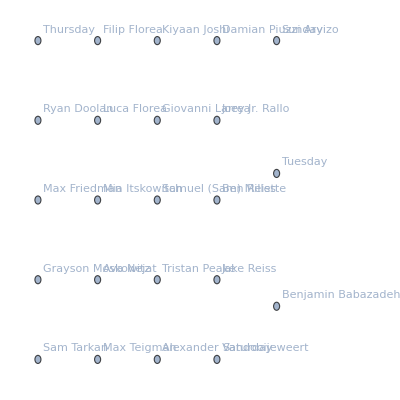

```mathematica
Graph[Join[winterSaturday[[All, 8]], {"Saturday", "Sunday", "Tuesday", "Thursday"}], {}, VertexLabels -> "Name", VertexCoordinates->]
```

```mathematica
winterSaturday
```

winterSaturday

Okay use the vertexcoordinates option to put the saturday sunday tuesday and thursday options to the right

Sure, here is the corrected code that includes the VertexCoordinatespaclet:ref/VertexCoordinates option to position the "Saturday", "Sunday", "Tuesday", and "Thursday" nodes to the right:

```mathematica
testGraph = Table[winterSaturday[[i, 8]]-> winterSaturday[[i, 9]], {i, 1, 19}]
testCoords = Join[Table[winterSaturday[[i, 8]]-> {0, i/4}, {i, 1, 19} ], {"Saturday"-> {4, 4}, "Sunday"-> {4,12 }, "Tuesday" -> {4, 8}, "Thursday"-> {4, 4}}]
```

{Benjamin Babazadeh→,Ryan Doolan→,Filip Florea→Saturday,Luca Florea→Saturday,Max Friedman→,Mia Itskowitch→Saturday,Kiyaan Joshi→Saturday,Giovanni Larrea→Saturday,Samuel (Sam) Millette→,Grayson Moskowitz→Saturday,Ava Nejat→Saturday,Tristan Peake→Saturday,Damian Piuzzi Arvizo→Saturday,Joey Jr. Rallo→,Ben Reiss→,Jake Reiss→,Sam Tarkan→,Max Teigman→Saturday,Alexander Vandooijeweert→}

{Benjamin Babazadeh→{0,1/4},Ryan Doolan→{0,1/2},Filip Florea→{0,3/4},Luca Florea→{0,1},Max Friedman→{0,5/4},Mia Itskowitch→{0,3/2},Kiyaan Joshi→{0,7/4},Giovanni Larrea→{0,2},Samuel (Sam) Millette→{0,9/4},Grayson Moskowitz→{0,5/2},Ava Nejat→{0,11/4},Tristan Peake→{0,3},Damian Piuzzi Arvizo→{0,13/4},Joey Jr. Rallo→{0,7/2},Ben Reiss→{0,15/4},Jake Reiss→{0,4},Sam Tarkan→{0,17/4},Max Teigman→{0,9/2},Alexander Vandooijeweert→{0,19/4},Saturday→{4,4},Sunday→{4,12},Tuesday→{4,8},Thursday→{4,4}}

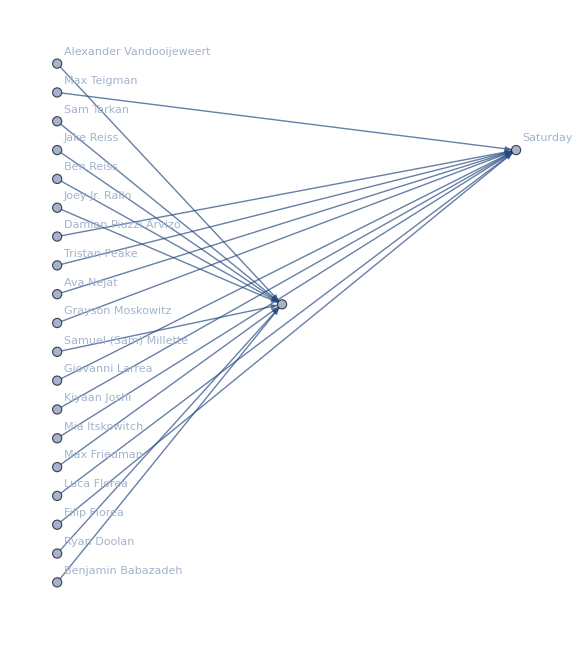

```mathematica
g = Graph[testGraph, VertexLabels->"Name", ImageSize->Large, VertexCoordinates->testCoords]
```

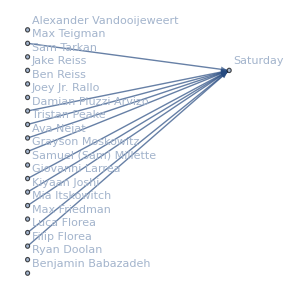

```mathematica
g =VertexDelete[g, ""]
```

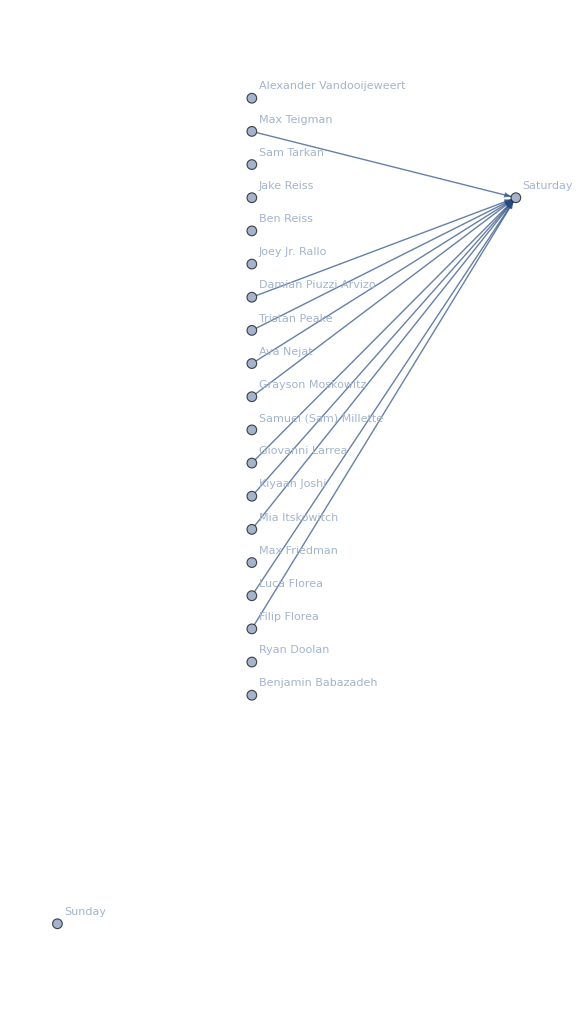

```mathematica
VertexAdd[g, "Sunday"]
```

```mathematica
testcoords = Table[i->{0, i}, {i, 1, 19}]
```

{1→{0,1},2→{0,2},3→{0,3},4→{0,4},5→{0,5},6→{0,6},7→{0,7},8→{0,8},9→{0,9},10→{0,10},11→{0,11},12→{0,12},13→{0,13},14→{0,14},15→{0,15},16→{0,16},17→{0,17},18→{0,18},19→{0,19}}

```mathematica
Length[winterSaturday]
```

19

```mathematica
Graph[Join[winterSaturday[[All,8]],{"Saturday","Sunday","Tuesday","Thursday"}],{},
    VertexLabels->"Name", ImageSize->Large, VertexCoordinates->testcoords]
```

Show[]

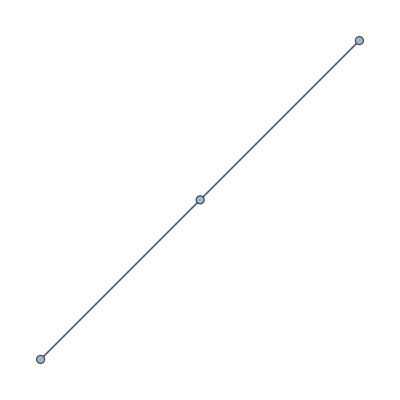

```mathematica
Graph[{1<->2,2<->3,3<->1},VertexCoordinates->{1->{0,0},2->{1,1}}]
```

```mathematica
VertexList[%80]
```

{Benjamin Babazadeh,Ryan Doolan,Filip Florea,Luca Florea,Max Friedman,Mia Itskowitch,Kiyaan Joshi,Giovanni Larrea,Samuel (Sam) Millette,Grayson Moskowitz,Ava Nejat,Tristan Peake,Damian Piuzzi Arvizo,Joey Jr. Rallo,Ben Reiss,Jake Reiss,Sam Tarkan,Max Teigman,Alexander Vandooijeweert,Saturday,Sunday,Tuesday,Thursday}

Now add 4 nodes which should be to the right: Saturday, Sunday, Tuesday, Thursday

To add the four nodes to the right of the graph, you can use the VertexCoordinateRulespaclet:ref/VertexCoordinateRules option. Here is the modified code: 
Graph[winterSaturday[[All, 8]], VertexLabels -> "Name", 
    VertexSize -> Medium, ImageSize -> Large, 
    VertexCoordinateRules -> Thread[{"Saturday", "Sunday", "Tuesday", "Thursday"} -> Range[4]]]

```mathematica
Graph[winterSaturday[[All, 8]], {}, VertexLabels -> "Name", 
    VertexSize -> Medium, ImageSize -> Large, 
    VertexCoordinateRules -> Thread[{"Saturday", "Sunday", "Tuesday", "Thursday"} -> Range[4]]]
```

Graph[winterSaturday[[All, 8]], {}, VertexLabels -> "Name", 
    VertexSize -> Medium, ImageSize -> Large, 
    VertexCoordinateRules -> Thread[{"Saturday", "Sunday", "Tuesday", "Thursday"} -> Range[4]]]

```mathematica
Graph[winterSaturday[[All, 8]], {}, VertexLabels->"Name", VertexCoordinates->Thread[{"Saturday, "}]]
```

```mathematica
Append[winterSaturday[[All, 8]], {"Saturday", "Sunday", "Tuesday", "Thursday"}]
```

{Benjamin Babazadeh,Ryan Doolan,Filip Florea,Luca Florea,Max Friedman,Mia Itskowitch,Kiyaan Joshi,Giovanni Larrea,Samuel (Sam) Millette,Grayson Moskowitz,Ava Nejat,Tristan Peake,Damian Piuzzi Arvizo,Joey Jr. Rallo,Ben Reiss,Jake Reiss,Sam Tarkan,Max Teigman,Alexander Vandooijeweert,{Saturday,Sunday,Tuesday,Thursday}}

Append the four days to the name list like above

To append the four days to the name list, you can use the Joinpaclet:ref/Join function. Here is the updated code: 
nameList = Join[winterSaturday[[All, 8]], {"Saturday", "Sunday", "Tuesday", "Thursday"}];

```mathematica
nameList = Join[winterSaturday[[All, 8]], {"Saturday", "Sunday", "Tuesday", "Thursday"}]
```

{Benjamin Babazadeh,Ryan Doolan,Filip Florea,Luca Florea,Max Friedman,Mia Itskowitch,Kiyaan Joshi,Giovanni Larrea,Samuel (Sam) Millette,Grayson Moskowitz,Ava Nejat,Tristan Peake,Damian Piuzzi Arvizo,Joey Jr. Rallo,Ben Reiss,Jake Reiss,Sam Tarkan,Max Teigman,Alexander Vandooijeweert,Saturday,Sunday,Tuesday,Thursday}